```mathematica
SetDirectory["/home/lukas/Dropbox/dev/tuberlin/epidemic-simulation/data"]
```

```mathematica
"/home/lukas/Dropbox/dev/tuberlin/epidemic-simulation/data"
```

/home/lukas/Dropbox/dev/tuberlin/epidemic-simulation/data

One dimensional

```mathematica
simData = Import["sim_data.csv"];
simDataColumns = simData // Transpose;
```

```mathematica
numberOfRuns = 10;
RR = (Plus @@ Table[simDataColumns[[c]], {c, 11, Length[simDataColumns], 8}] // Rest) / numberOfRuns //N;

pInfection = simDataColumns[[1]] // Rest;
RR = (Table[simDataColumns[[c]] // Rest, {c, 11, Length[simDataColumns], 8}] // Rest) ;

data = Table[ {pInfection, RR[[c]]} // Transpose,  {c, 1, Length[RR]}] // Join;
data = Flatten[data, 1];
```

```mathematica
RRAverage = (Plus @@ Table[simDataColumns[[c]], {c, 11, Length[simDataColumns], 8}] // Rest) / numberOfRuns //N;

RRSTD = Map[StandardDeviation,(Table[simDataColumns[[c]] // Rest, {c, 11, Length[simDataColumns], 8}] // Rest)] //N;
```

```mathematica
x[[1]]
```

{ RR_1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,194,0,0,0,0,0,0,0,0,0,0,850,0,0,0,274,9103,0,0,8788,8709,0,0,0,0,0,409,0,0,58,0,86,5,0,423,8982,9000,8651,0,0,1,0,9139,1,9008,0,9251,9127,25,108,167,50,9265,42,39,17,8655,9023,0,1,9391,5,13,9249,9360,44,9167,2,9294,3,2,9343,9116,11,2,9223,9172,9391,4,9252,4,0,34,1,9099,9269,9424,9360,9500,9197,2,1,9364,9240,9387,9261,9426,1,9415,9324,9391,9450,1,9239,9380,9384,1,1,9334,9500,9460,9376,9472,9517,7,9449,9501,9404,9397,9448,9485,9383,9608,9646,9428,9515,1,9471,9582,9504,9547,9510,9525,9569,9550,9538,9532,9583,9725,9541,1,9625,9677,9632,9620}

```mathematica
ListPlot[ data]
```

-Graphics-

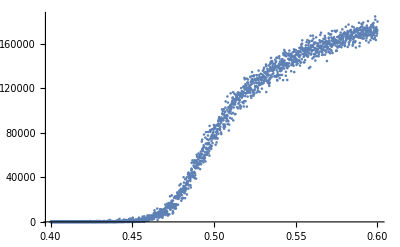

```mathematica
Needs["ErrorBarPlots`"]
ListPlot[ {pInfection, RRAverage} // Transpose]
```

```mathematica
RR
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.1,1.7,3667.4,10605.9,18231.,15614.2,19001.7,22632.7,30097.6,30245.4,30175.4,34198.7,34350.9,38338.7,27004.6,38685.4,38876.9,38981.4,35217.1,39235.6,35405.6,35491.,35560.5,39575.,39634.9,39695.7,39740.5,39784.1,39825.7,39854.,39877.4,39903.,39914.4,39930.9,39944.8,39957.2,39965.8,39973.7,39977.3,39982.1,39987.1,39991.,39994.9,39994.6,39996.5,39997.8,39999.3,39999.1,39999.6,39999.5,40000.,40000.,40000.,40000.}

Two dimensional

```mathematica
simData = Import["sim_data_2d.csv"];
simDataColumns = simData // Transpose;
```

```mathematica
numberOfRuns = 100;
di = 0.1;
dc = 0.1;
minI = 0;
maxI = 1;
minC = 0;
maxC = 1;

extractRR[d_] := (Plus @@ Table[  d[[c]] , {c, 11, Length[d], 8}] ) / numberOfRuns //N;

dat = Table[  extractRR[Select[simData, #[[1]] == i && #[[2]] == c &][[1]] ], {i, minI, maxI, di}, {c, minC, maxC, dc}];
```

```mathematica
ListPointPlot3D[dat]
```

-Graphics3D-